```mathematica
bitcoinPrice = Quantity[10000, "USDollars"];
satPrice = bitcoinPrice / 100000000;
txfee = Quantity[20, 1/"Bytes"];
energycost = Quantity[0.13, "USDollars" / "Kilowatts" / "Hours"];
```

#### Table 5.1

```mathematica
txSize[scriptSize_, numScripts_] := Module[{tinsize, toutsize, tsize}, 
tinsize = 36 + 1 + 180 + 4;
toutsize = 8 + 1 + scriptSize; 
tsize = 4+1+tinsize+3+numScripts*toutsize; (* assuming numScripts in [253,65535] *)
tsize];
```

```mathematica
scriptSize = <| "p2pk" -> Quantity[1 + 32 + 1 + 1, "Bytes"], "p2ms" -> Quantity[1 + (1 + 1 + 32) * 3 + 2, "Bytes"],"p2pkh" -> Quantity[2 + 1 + 20 + 2, "Bytes"],
"p2sh" -> Quantity[1 + 1 + 20 + 1, "Bytes"] ,
"p2fms" -> Quantity[1 + (1 + 1 + 64) * 3 + 2, "Bytes"]|>
```

<|p2pk→35 B,p2ms→105 B,p2pkh→25 B,p2sh→23 B,p2fms→201 B|>

```mathematica
numScripts = Map[Module[{tsize},
tsize = txSize[# / Quantity["Bytes"], n];
Floor[n] /. FindMaximum[{tsize, tsize ≤ 100000}, {n}][[2]]
] &]@scriptSize;
numScripts[["p2ms"]] = 16000/80;  (* constrained by MAX_STANDARD_TX_SIGOPS_COST *)
numScripts[["p2fms"]] = 16000/80;
numScripts
```

<|p2pk→2267,p2ms→200,p2pkh→2934,p2sh→3117,p2fms→200|>

```mathematica
numAddresses = Map[Identity]@numScripts;
numAddresses[["p2ms"]] = 3*numAddresses[["p2ms"]];
numAddresses[["p2fms"]] = 3*numAddresses[["p2fms"]];
numAddresses
```

<|p2pk→2267,p2ms→600,p2pkh→2934,p2sh→3117,p2fms→600|>

```mathematica
(*bytesPerAddress = AssociationMap[ N@Quantity[txSize[scriptSize[[#]]/ Quantity["Bytes"], numScripts[[#]]], "Bytes"]/ numScripts[[#]]&]@Keys[scriptSize]*)
```

```mathematica
totalFee = AssociationMap[Module[{tsize}, 
tsize = txSize[scriptSize[[#]]/ Quantity["Bytes"], numScripts[[#]]];
Quantity[tsize, "Bytes"] * txfee + numScripts[[#]] * (scriptSize[[#]]/ Quantity["Bytes"]+ 157)*3
] &]@Keys[scriptSize];
totalFee
```

<|p2pk→3305332,p2ms→617780,p2pkh→3601664,p2sh→3682640,p2fms→1059380|>

```mathematica
fValue = totalFee / numAddresses;
fValue = Dataset@Map[<| "usdf" -> # * satPrice, "satf" -> # |> &]@fValue;
fValue[All, {"usdf" -> (N[QuantityMagnitude[#], 3] &), "satf" -> (N[#, 6] &)}]
```

Dataset[<>]

Nondust vs Recovery: p2sh

```mathematica
Module[{tinsize, toutsize, tsize, nondust}, 
tinsize = 36 + 1 + 71 + 4;
toutsize = 8 + 1 + 23; 
tsize = 4+3+n*tinsize+1+toutsize; (* assuming numScripts in [253,65535] *)
nondust = n * (scriptSize[["p2pk"]]/ Quantity["Bytes"]+ 157)*3;
N[nondust/tsize] /. n -> Floor@Last@Last@FindMaximum[{tsize, tsize ≤ 100000}, {n}][[2]]
]
```

5.1408

Nondust vs Recovery: p2ms (count sigops)

```mathematica
Module[{tinsize, toutsize, tsize, nondust, sigopCost}, 
tinsize = 36 + 1 + 71 + 4;
toutsize = 8 + 1 + 23; 
tsize = 4+3+n*tinsize+1+toutsize; (* assuming numScripts in [253,65535] *)
sigopCost = 20*n*20;
nondust = n * (scriptSize[["p2ms"]]/ Quantity["Bytes"]+ 157)*3;
N@{nondust/sigopCost, nondust/tsize}
]
```

{1.965,(786. n)/(40.+112. n)}

#### Table 5.2

```mathematica
performancesTable = SemanticImport[FileNameJoin[{NotebookDirectory[],"./performances.csv"}]][All, {"wattage" -> (Quantity[#, "Watts"] &), "frequency" -> (Quantity[#, "Megaherz"] &) }];
```

```mathematica
performancesTable[All, Append[#, "c" -> UnitConvert[#wattage / #frequency* energycost, "USDollars"]] &]
```

Dataset[<>]

#### Figure 5.1

```mathematica
cEstimate = <| "p2pk" -> Quantity[4.5 10^-15, "USDollars"], "p2ms" -> Quantity[4.5 10^-15, "USDollars"],"p2pkh" -> Quantity[4.5 10^-15, "USDollars"],
"p2sh" -> Quantity[3.00 10^-15, "USDollars"]|>
payloadLength = Quantity[10, "kiloBytes"];
```

<|p2pk→4.50×10^-15 $,p2ms→4.50×10^-15 $,p2pkh→4.50×10^-15 $,p2sh→3.00×10^-15 $|>

```mathematica
Cost[n_, N_, c_, f_] := Module[{m}, m = N / Quantity[n, "Bits"];
2^n * HarmonicNumber[m] * c + f * m
];
```

```mathematica
plotFunctions = AssociationMap[Function[n, Cost[n, payloadLength, cEstimate[[#]], fValue[[#]][["usdf"]]]/ payloadLength * Quantity["Kilobyte"] / Quantity["USDollars"] ] &]@Keys[cEstimate];
plotFunctions = Append[plotFunctions, "p2fms"-> Function[n, Cost[65 * 8, payloadLength, 0, fValue[["p2fms"]][["usdf"]]]/ payloadLength * Quantity["Kilobyte"] / Quantity["USDollars"]]];
```

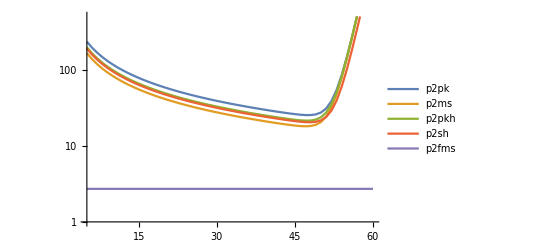

```mathematica
Module[{datapoints, range},
range = {5, 60};
datapoints = Merge[Table[Map[{n, #[n]} &]@plotFunctions, {n,range[[1]], range[[2]]}], Identity];
ListLogPlot[datapoints, Joined->True, PlotRange->{range, {1, 500}}]
]
```

```mathematica
Export["/home/anton/Dokumente/JMU Inf MSc/itsec-praktikum/report/plot1.csv",Prepend[Flatten@{Keys@plotFunctions, "n"}]@Transpose@Append[Range[5, 60]]@Values@Map[Last]@Map[Transpose]@N@Merge[Table[Map[{n, #[n]} &]@plotFunctions, {n,5, 60}], Identity], "CSV"]
```

/home/anton/Dokumente/JMU Inf MSc/itsec-praktikum/report/plot1.csv

```mathematica
baseline = Quantity[plotFunctions[["p2fms"]][_], "USDollars" / "Kilobytes"] // N
```

2.71636 $

#### Table 5.3

```mathematica
optimums = Module[{datapoints, opt, table},
datapoints = Merge[Table[Map[{n, #[n]} &]@plotFunctions, {n,5, 55}], Identity][[{"p2pk", "p2ms", "p2pkh", "p2sh"}]];
opt = Map[First@*SortBy[Last]]@datapoints;
table = Dataset[Map[<| "n" -> First[#], "cost" -> Quantity[Last[#], "USDollars" / "Kilobytes"] |> &]@opt];
table[All, Append[#, "increase" -> #cost / baseline] &]
]
```

Dataset[<>]

```mathematica
computationTime = UnitConvert[Module[{n, m, N}, 
N = payloadLength;
n = optimums["p2sh"]["n"]; 
m = N / Quantity[n, "Bits"];
2^n * HarmonicNumber[m]
] / Quantity[3700, "Megahertz"], "Hours"] // N
```

168.972 h

#### Figure 5.2

```mathematica
Cp2ms[p_, c_] := Module[{costfn},
costfn = SetPrecision[Cost[n, payloadLength, c, fValue[["p2ms"]][["satf"]] * p / 10^8], 100];
First@FindMinimum[costfn, {n, 10}] / payloadLength
]
Cp2ms[bitcoinPrice, Quantity[5 10^-15, "USDollars"]]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

18.0893 $

```mathematica
Cp2fms[p_] := Cost[65 * 8, payloadLength, 0, fValue[["p2fms"]][["satf"]] * p / 10^8] / payloadLength;
Cp2fms[bitcoinPrice] // N
```

2.71636 $

```mathematica
Off[FindMinimum::lstol];
modelPoints = N@Curry[Flatten][1]@Table[Block[{c = Quantity[10^cc, "USDollars"], p = Quantity[10^pp, "USDollars"]},
{p, c, Cp2ms[p, c]}
], {cc, -20, -14, .2}, {pp, 3, 6, .2}];
```

```mathematica
normalized = Log10[Map[{#[[1]] / Quantity["USDollar"], #[[2]] / Quantity["USDollar"], #[[3]]  / Quantity["USDollar"]*Quantity["Bytes"]} &]@modelPoints];
Dimensions[normalized]
```

{496,3}

```mathematica
fit = LinearModelFit[normalized, {p, c}, {p, c}]
```

FittedModel[-5.29006+0.0249485 c+0.974982 p]

```mathematica
{α, β, γ} = fit["BestFitParameters"]
```

{-5.29006,0.974982,0.0249485}

```mathematica
Max@Abs@fit["FitResiduals"]
PercentForm[10^Max@Abs@fit["FitResiduals"] - 1]
fit["ANOVATable"]
```

0.0124968

2.919%

General::munfl: Exp[-2806.45] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1327.23] is too small to represent as a normalized machine number; precision may be lost.

| DF | SS | MS | F-Statistic | P-Value
p | 1 | 400.769 | 400.769 | 4.28062×10^7 | 0.
c | 1 | 0.987914 | 0.987914 | 105519. | 0.
Error | 493 | 0.00461567 | 9.36241×10^-6 |  | 
Total | 495 | 401.762 |  |  |

```mathematica
Show[Plot3D[fit["BestFit"],{p,3, 6},{c, -20, -14}, PlotStyle->Directive[Opacity[0.5]],MeshFunctions->{#3&},Mesh->10], ListPointPlot3D[normalized]]
```

-Graphics3D-

Decrease on relative inclusion cost on 100-fold price increase,  Decrease 10-fold performance increase

```mathematica
PercentForm[(10^(Log10[100] β) - 100)/100]
```

-10.88%

```mathematica
PercentForm[10^(Log10[1/10] γ) - 1]
```

-5.583%

```mathematica
MinMax@Map[#[[3]] / Cp2fms[#[[1]]] &, modelPoints]
```

{4.3342,7.31342}

```mathematica
Log2[10] * 2 // N
```

6.64386

{0.00229437 p^0.974982,0.00204535 p^0.974982,0.00182335 p^0.974982,0.00162545 p^0.974982,(52969 p)/195000000}

/home/anton/Dokumente/JMU Inf MSc/itsec-praktikum/report/plot2-points.csv

/home/anton/Dokumente/JMU Inf MSc/itsec-praktikum/report/plot2-fit.csv

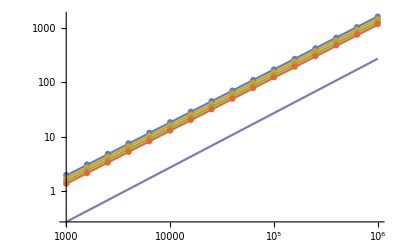

```mathematica
cSamples = {10^(-14), 10^(-16), 10^(-18), 10^(-20)};
fitFormulas = Table[Evaluate[1000 10^(fit["BestFit"]) /. {p-> Log10[p], c->Log10[c]}], {c, cSamples}] ~ Append ~ (Cp2fms[p]*Quantity["Kilobytes"])
samplePoints = Table[Map[{#[[1]]/Quantity["USDollar"], #[[3]]/ Quantity["USDollars" / "Kilobytes"]} &]@Select[x == QuantityMagnitude@#[[2]] &][modelPoints], {x, cSamples}];
Export["/home/anton/Dokumente/JMU Inf MSc/itsec-praktikum/report/plot2-points.csv",Map[Map[Last,#]~Prepend~ First@First[#] &]@Transpose@samplePoints, "CSV"]
Export["/home/anton/Dokumente/JMU Inf MSc/itsec-praktikum/report/plot2-fit.csv",N@Table[Evaluate[Prepend[p]@fitFormulas], {p, {10^3, 10^6}}], "CSV"]
Show[LogLogPlot[fitFormulas, {p, 10^(3), 10^(6)}], ListLogLogPlot[samplePoints]]
```

/home/anton/Dokumente/JMU Inf MSc/itsec-praktikum/report/plot3-points.csv

/home/anton/Dokumente/JMU Inf MSc/itsec-praktikum/report/plot3-fit.csv

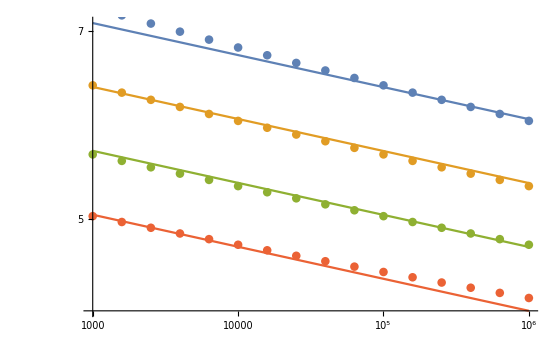

```mathematica
fitFormulasRel = fitFormulas[[1;;4]] / fitFormulas[[5]];
samplePointsRel = Table[Map[{#[[1]]/Quantity["USDollar"], #[[3]]/Cp2fms[#[[1]]] } &]@Select[x == QuantityMagnitude@#[[2]] &][modelPoints], {x, cSamples}];
Export["/home/anton/Dokumente/JMU Inf MSc/itsec-praktikum/report/plot3-points.csv",Map[Map[Last,#]~Prepend~ First@First[#] &]@Transpose@samplePointsRel, "CSV"]
Export["/home/anton/Dokumente/JMU Inf MSc/itsec-praktikum/report/plot3-fit.csv",N@Table[Evaluate[Prepend[p]@fitFormulasRel], {p, {10^3, 10^6}}], "CSV"]
Show[LogLogPlot[fitFormulasRel, {p, 10^(3), 10^(6)}], ListLogLogPlot[samplePointsRel]]
```